```mathematica
ρ=DiagonalMatrix[{1,0,0,0}];
```

```mathematica
H=Array[Subscript[h, #1,#2]&,{4,4}];
```

```mathematica
cm[A_,B_]:=A.B-B.A;
am[A_,B_]:=A.B+B.A;
```

```mathematica
cm[H,ρ]//MatrixForm
```

(0 | -h_(1,2) | -h_(1,3) | -h_(1,4)
h_(2,1) | 0 | 0 | 0
h_(3,1) | 0 | 0 | 0
h_(4,1) | 0 | 0 | 0)

```mathematica
TrB[X_]:=Map[Tr,Partition[X,{2,2}],{2}]
```

```mathematica
TrB[Nest[cm[H,#]&,ρ,2]]//Simplify//MatrixForm
```

(2 (h_(1,3) h_(3,1)+h_(1,4) h_(4,1)) | -h_(1,1) h_(1,3)+h_(1,2) h_(2,3)+h_(1,3) h_(3,3)+h_(1,4) (-2 h_(2,1)+h_(4,3))
-h_(1,1) h_(3,1)+h_(2,1) h_(3,2)+h_(3,1) h_(3,3)-2 h_(1,2) h_(4,1)+h_(3,4) h_(4,1) | -2 (h_(1,3) h_(3,1)+h_(1,4) h_(4,1)))

```mathematica
TrB[cm[H,cm[H,ρ]]]/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0}//MatrixForm
```

(0 | h_(1,2) h_(2,3)
h_(2,1) h_(3,2) | 0)

```mathematica
H/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0}//MatrixForm
```

(h_(1,1) | h_(1,2) | 0 | 0
h_(2,1) | h_(2,2) | h_(2,3) | h_(2,4)
0 | h_(3,2) | h_(3,3) | h_(3,4)
0 | h_(4,2) | h_(4,3) | h_(4,4))

```mathematica
TrB[Nest[cm[H,#]&,ρ,3]][[1,1]]//Simplify
```

-3 h_(1,2) (h_(2,3) h_(3,1)+h_(2,4) h_(4,1))+3 h_(2,1) (h_(1,3) h_(3,2)+h_(1,4) h_(4,2))

```mathematica
TrB[Nest[cm[H,#]&,ρ,3]][[1,1]]/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0}
```

0

```mathematica
TrB[Nest[cm[H,#]&,ρ,4]][[1,1]]//Simplify
```

2 (4 h_(1,3)^2 h_(3,1)^2+2 h_(1,3) h_(2,1) h_(2,2) h_(3,2)+4 h_(1,3) h_(2,3) h_(3,1) h_(3,2)-h_(1,3) h_(2,1) h_(3,2) h_(3,3)+h_(1,3) h_(3,1) h_(3,3)^2+8 h_(1,3) h_(1,4) h_(3,1) h_(4,1)+4 h_(1,3) h_(2,4) h_(3,2) h_(4,1)+h_(1,3) h_(3,3) h_(3,4) h_(4,1)+4 h_(1,4)^2 h_(4,1)^2+h_(1,1)^2 (h_(1,3) h_(3,1)+h_(1,4) h_(4,1))+2 h_(1,4) h_(2,1) h_(2,2) h_(4,2)+4 h_(1,4) h_(2,3) h_(3,1) h_(4,2)-h_(1,3) h_(2,1) h_(3,4) h_(4,2)+4 h_(1,4) h_(2,4) h_(4,1) h_(4,2)-h_(1,4) h_(2,1) h_(3,2) h_(4,3)+h_(1,4) h_(3,1) h_(3,3) h_(4,3)+h_(1,3) h_(3,1) h_(3,4) h_(4,3)+h_(1,4) h_(3,4) h_(4,1) h_(4,3)+h_(1,3) h_(3,4) h_(4,1) h_(4,4)-h_(1,4) h_(2,1) h_(4,2) h_(4,4)+h_(1,4) h_(3,1) h_(4,3) h_(4,4)+h_(1,4) h_(4,1) h_(4,4)^2+h_(1,2) (4 h_(1,3) h_(2,1) h_(3,1)-3 h_(2,1) h_(2,3) h_(3,2)-h_(2,3) h_(3,1) h_(3,3)+4 h_(1,4) h_(2,1) h_(4,1)-h_(2,3) h_(3,4) h_(4,1)+2 h_(2,2) (h_(2,3) h_(3,1)+h_(2,4) h_(4,1))-3 h_(2,1) h_(2,4) h_(4,2)-h_(2,4) h_(3,1) h_(4,3)-h_(2,4) h_(4,1) h_(4,4))-h_(1,1) (h_(1,2) (h_(2,3) h_(3,1)+h_(2,4) h_(4,1))+h_(1,3) (h_(2,1) h_(3,2)+2 h_(3,1) h_(3,3)+2 h_(3,4) h_(4,1))+h_(1,4) (h_(2,1) h_(4,2)+2 h_(3,1) h_(4,3)+2 h_(4,1) h_(4,4))))

```mathematica
TrB[Nest[cm[H,#]&,ρ,4]][[1,1]]/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0}//Simplify
```

-6 h_(1,2) h_(2,1) (h_(2,3) h_(3,2)+h_(2,4) h_(4,2))

```mathematica
TrB[Nest[cm[H/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0},#]&,ρ,7]][[1,1]]//Simplify
```

0

```mathematica
{σ[0],σ[1],σ[2],σ[3]}=Table[PauliMatrix[i]/√2,{i,0,3}];
```

```mathematica
σ[1]
```

{{0,1/(√2)},{1/(√2),0}}

```mathematica
H1=Sum[√2 σ[i] Subscript[B, i],{i,1,3}]//Simplify
```

{{B_3,B_1-ⅈ B_2},{B_1+ⅈ B_2,-B_3}}

```mathematica
cm[H1,cm[H1,{{ρB,0},{0,0}}]]//MatrixForm
```

(2 ρB (B_1-ⅈ B_2) (B_1+ⅈ B_2) | -2 ρB (B_1-ⅈ B_2) B_3
-2 ρB (B_1+ⅈ B_2) B_3 | -2 ρB (B_1-ⅈ B_2) (B_1+ⅈ B_2))

```mathematica
B[1]={{0,√(1/8)t},{√(1/8)t,√(1/8)tt}};
B[2]={{0,-ⅈ √(1/8)t},{ⅈ √(1/8)t,0}};
B[3]=B[1];
```

```mathematica
Sum[Tr[B[i].B[i]],{i,1,3}]
```

(3 t^2)/4+t^4/4

```mathematica
HermitianMatrixQ/@{B[1],B[2],B[3]}
```

{False,False,False}

```mathematica
Ht=Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}]//Simplify;
MatrixForm[Ht]
```

(0 | t/4 | 0 | 0
t/4 | tt/4 | t/2 | tt/4
0 | t/2 | 0 | -t/4
0 | tt/4 | -t/4 | -tt/4)

```mathematica
1/√2{1,0,0,1}.{σ[0],σ[1],σ[2],σ[3]}
```

{{1,0},{0,0}}

```mathematica
Nest[cm[Ht,#]&,ρ,1]//Simplify//MatrixForm
```

(0 | -t/4 | 0 | 0
t/4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
TrB[Nest[cm[Ht,#]&,ρ,2]]//Simplify
```

{{0,1/8},{1/8,0}}

```mathematica
TrB[Nest[cm[Ht,#]&,ρ,4]]//Simplify
```

{{-3/128 t^2 (4 t^2+tt^2),t^4/8+(5 t^2 tt^2)/128},{t^4/8+(5 t^2 tt^2)/128,3/128 t^2 (4 t^2+tt^2)}}

```mathematica
-3/128 t^2 (4 t^2+tt^2)/.{t->1,tt->1}
```

-15/128

```mathematica
-15/128*1/24
```

-5/1024

```mathematica
Total[Array[Subscript[b, #1,#2]^2&,{3,4},{1,0}],2]
```

b_(1,0)^2+b_(1,1)^2+b_(1,2)^2+b_(1,3)^2+b_(2,0)^2+b_(2,1)^2+b_(2,2)^2+b_(2,3)^2+b_(3,0)^2+b_(3,1)^2+b_(3,2)^2+b_(3,3)^2

```mathematica
Array[Subscript[b, #1,#2]&,{3,4},{1,0}]//Flatten
```

{b_(1,0),b_(1,1),b_(1,2),b_(1,3),b_(2,0),b_(2,1),b_(2,2),b_(2,3),b_(3,0),b_(3,1),b_(3,2),b_(3,3)}

```mathematica
{B[0],B[1],B[2],B[3]}=Array[Subscript[b, #1,#2]&,{4,4},0].Table[σ[i],{i,0,3}]/.{Subscript[b, 0,0]->0};
Ht=Sum[KroneckerProduct[σ[i],B[i]],{i,0,3}]//Simplify;
MatrixForm[Ht]
```

(1/2 (b_(0,3)+b_(3,0)+b_(3,3)) | 1/2 (b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))) | 1/2 (b_(1,0)+b_(1,3)-ⅈ (b_(2,0)+b_(2,3))) | 1/2 (b_(1,1)-ⅈ (b_(1,2)+b_(2,1)-ⅈ b_(2,2)))
1/2 (b_(0,1)+ⅈ b_(0,2)+b_(3,1)+ⅈ b_(3,2)) | 1/2 (-b_(0,3)+b_(3,0)-b_(3,3)) | 1/2 (b_(1,1)+ⅈ b_(1,2)-ⅈ b_(2,1)+b_(2,2)) | 1/2 (b_(1,0)-b_(1,3)-ⅈ (b_(2,0)-b_(2,3)))
1/2 (b_(1,0)+b_(1,3)+ⅈ (b_(2,0)+b_(2,3))) | 1/2 (b_(1,1)-ⅈ b_(1,2)+ⅈ b_(2,1)+b_(2,2)) | 1/2 (b_(0,3)-b_(3,0)-b_(3,3)) | 1/2 (b_(0,1)-ⅈ b_(0,2)-b_(3,1)+ⅈ b_(3,2))
1/2 (b_(1,1)+ⅈ (b_(1,2)+b_(2,1)+ⅈ b_(2,2))) | 1/2 (b_(1,0)-b_(1,3)+ⅈ (b_(2,0)-b_(2,3))) | 1/2 (b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))) | 1/2 (-b_(0,3)-b_(3,0)+b_(3,3)))

```mathematica
tt=Simplify[Norm[KroneckerProduct[σ[0],B[0]]+ KroneckerProduct[σ[3],B[3]]],{Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3]}∈ Reals]
```

Max[1/(2 √2)(√(Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] b_(0,1)+b_(0,1)^2+ⅈ Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] b_(0,2)+b_(0,2)^2+2 b_(0,3)^2+2 b_(3,0)^2-Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] b_(3,1)-2 b_(0,1) b_(3,1)+b_(3,1)^2-ⅈ b_(0,1) b_(3,2)-3 b_(0,2) b_(3,2)+ⅈ b_(3,1) b_(3,2)+2 b_(3,2)^2-4 b_(0,3) b_(3,3)+2 b_(3,3)^2-√(-4 (b_(0,3)^2-b_(3,0)^2+Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] (b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2)))-2 b_(0,3) b_(3,3)+b_(3,3)^2) (b_(0,1)^2+b_(0,2)^2+b_(0,3)^2-b_(3,0)^2-2 b_(0,1) b_(3,1)+b_(3,1)^2-2 b_(0,2) b_(3,2)+b_(3,2)^2-2 b_(0,3) b_(3,3)+b_(3,3)^2)+(b_(0,1)^2+b_(0,2)^2+2 b_(0,3)^2+2 b_(3,0)^2+Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] (b_(0,1)+ⅈ b_(0,2)-b_(3,1))+b_(3,1)^2-b_(0,1) (2 b_(3,1)+ⅈ b_(3,2))-3 b_(0,2) b_(3,2)+ⅈ b_(3,1) b_(3,2)+2 b_(3,2)^2-4 b_(0,3) b_(3,3)+2 b_(3,3)^2)^2))),1/(2 √2)(√(Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] b_(0,1)+b_(0,1)^2+ⅈ Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] b_(0,2)+b_(0,2)^2+2 b_(0,3)^2+2 b_(3,0)^2-Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] b_(3,1)-2 b_(0,1) b_(3,1)+b_(3,1)^2-ⅈ b_(0,1) b_(3,2)-3 b_(0,2) b_(3,2)+ⅈ b_(3,1) b_(3,2)+2 b_(3,2)^2-4 b_(0,3) b_(3,3)+2 b_(3,3)^2+√(-4 (b_(0,3)^2-b_(3,0)^2+Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] (b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2)))-2 b_(0,3) b_(3,3)+b_(3,3)^2) (b_(0,1)^2+b_(0,2)^2+b_(0,3)^2-b_(3,0)^2-2 b_(0,1) b_(3,1)+b_(3,1)^2-2 b_(0,2) b_(3,2)+b_(3,2)^2-2 b_(0,3) b_(3,3)+b_(3,3)^2)+(b_(0,1)^2+b_(0,2)^2+2 b_(0,3)^2+2 b_(3,0)^2+Conjugate[b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))] (b_(0,1)+ⅈ b_(0,2)-b_(3,1))+b_(3,1)^2-b_(0,1) (2 b_(3,1)+ⅈ b_(3,2))-3 b_(0,2) b_(3,2)+ⅈ b_(3,1) b_(3,2)+2 b_(3,2)^2-4 b_(0,3) b_(3,3)+2 b_(3,3)^2)^2))),1/(2 √2)(√(Conjugate[b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))] b_(0,1)+b_(0,1)^2-ⅈ b_(0,1) b_(0,2)+2 b_(0,2)^2+2 b_(0,3)^2+2 b_(3,0)^2+Conjugate[b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))] b_(3,1)+2 b_(0,1) b_(3,1)-ⅈ b_(0,2) b_(3,1)+b_(3,1)^2-ⅈ b_(0,1) b_(3,2)+4 b_(0,2) b_(3,2)-ⅈ b_(3,1) b_(3,2)+2 b_(3,2)^2+4 b_(0,3) b_(3,3)+2 b_(3,3)^2-√(-4 (b_(0,1)^2+b_(0,2)^2+b_(0,3)^2-b_(3,0)^2+2 b_(0,1) b_(3,1)+b_(3,1)^2+2 b_(0,2) b_(3,2)+b_(3,2)^2+2 b_(0,3) b_(3,3)+b_(3,3)^2) (b_(0,3)^2-b_(3,0)^2-ⅈ Conjugate[b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))] (b_(0,2)+ⅈ (b_(0,1)+b_(3,1))+b_(3,2))+2 b_(0,3) b_(3,3)+b_(3,3)^2)+(b_(0,1)^2+2 b_(0,2)^2+2 b_(0,3)^2+2 b_(3,0)^2-ⅈ b_(0,2) b_(3,1)+b_(3,1)^2+Conjugate[b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))] (b_(0,1)+b_(3,1))+4 b_(0,2) b_(3,2)-ⅈ b_(3,1) b_(3,2)+2 b_(3,2)^2-ⅈ b_(0,1) (b_(0,2)+2 ⅈ b_(3,1)+b_(3,2))+4 b_(0,3) b_(3,3)+2 b_(3,3)^2)^2))),1/(2 √2)(√(Conjugate[b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))] b_(0,1)+b_(0,1)^2-ⅈ b_(0,1) b_(0,2)+2 b_(0,2)^2+2 b_(0,3)^2+2 b_(3,0)^2+Conjugate[b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))] b_(3,1)+2 b_(0,1) b_(3,1)-ⅈ b_(0,2) b_(3,1)+b_(3,1)^2-ⅈ b_(0,1) b_(3,2)+4 b_(0,2) b_(3,2)-ⅈ b_(3,1) b_(3,2)+2 b_(3,2)^2+4 b_(0,3) b_(3,3)+2 b_(3,3)^2+√(-4 (b_(0,1)^2+b_(0,2)^2+b_(0,3)^2-b_(3,0)^2+2 b_(0,1) b_(3,1)+b_(3,1)^2+2 b_(0,2) b_(3,2)+b_(3,2)^2+2 b_(0,3) b_(3,3)+b_(3,3)^2) (b_(0,3)^2-b_(3,0)^2-ⅈ Conjugate[b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))] (b_(0,2)+ⅈ (b_(0,1)+b_(3,1))+b_(3,2))+2 b_(0,3) b_(3,3)+b_(3,3)^2)+(b_(0,1)^2+2 b_(0,2)^2+2 b_(0,3)^2+2 b_(3,0)^2-ⅈ b_(0,2) b_(3,1)+b_(3,1)^2+Conjugate[b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))] (b_(0,1)+b_(3,1))+4 b_(0,2) b_(3,2)-ⅈ b_(3,1) b_(3,2)+2 b_(3,2)^2-ⅈ b_(0,1) (b_(0,2)+2 ⅈ b_(3,1)+b_(3,2))+4 b_(0,3) b_(3,3)+2 b_(3,3)^2)^2)))]

```mathematica
NMaximize[{tt,
Subscript[b, 0,1]^2+Subscript[b, 0,2]^2+Subscript[b, 0,3]^2==1&&Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2==1},{Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3]}]
```

```mathematica
Simplify[Norm[α KroneckerProduct[σ[0],σ[0]]+β KroneckerProduct[σ[3],σ[0]]],α≥ 0&&β≥ 0]
```

(α+β)/2

```mathematica
Simplify[Norm[KroneckerProduct[σ[0],B[0]]],{Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3]}∈ Reals]
```

1/2 √(b_(0,1)^2+b_(0,2)^2+b_(0,3)^2)

```mathematica
h2b=Flatten[MapThread[#1->#2&,{H,Ht},2]]
```

{h_(1,1)→1/2 (b_(0,0)+b_(0,3)+b_(3,0)+b_(3,3)),h_(1,2)→1/2 (b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))),h_(1,3)→1/2 (b_(1,0)+b_(1,3)-ⅈ (b_(2,0)+b_(2,3))),h_(1,4)→1/2 (b_(1,1)-ⅈ (b_(1,2)+b_(2,1)-ⅈ b_(2,2))),h_(2,1)→1/2 (b_(0,1)+ⅈ b_(0,2)+b_(3,1)+ⅈ b_(3,2)),h_(2,2)→1/2 (b_(0,0)-b_(0,3)+b_(3,0)-b_(3,3)),h_(2,3)→1/2 (b_(1,1)+ⅈ b_(1,2)-ⅈ b_(2,1)+b_(2,2)),h_(2,4)→1/2 (b_(1,0)-b_(1,3)-ⅈ (b_(2,0)-b_(2,3))),h_(3,1)→1/2 (b_(1,0)+b_(1,3)+ⅈ (b_(2,0)+b_(2,3))),h_(3,2)→1/2 (b_(1,1)-ⅈ b_(1,2)+ⅈ b_(2,1)+b_(2,2)),h_(3,3)→1/2 (b_(0,0)+b_(0,3)-b_(3,0)-b_(3,3)),h_(3,4)→1/2 (b_(0,1)-ⅈ b_(0,2)-b_(3,1)+ⅈ b_(3,2)),h_(4,1)→1/2 (b_(1,1)+ⅈ (b_(1,2)+b_(2,1)+ⅈ b_(2,2))),h_(4,2)→1/2 (b_(1,0)-b_(1,3)+ⅈ (b_(2,0)-b_(2,3))),h_(4,3)→1/2 (b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))),h_(4,4)→1/2 (b_(0,0)-b_(0,3)-b_(3,0)+b_(3,3))}

```mathematica
Table[1/2 Tr[Ht.KroneckerProduct[σ[i],σ[j]]]//Simplify,{i,0,3},{j,0,3}]
```

{{b_(0,0),b_(0,1),b_(0,2),b_(0,3)},{b_(1,0),b_(1,1),b_(1,2),b_(1,3)},{b_(2,0),b_(2,1),b_(2,2),b_(2,3)},{b_(3,0),b_(3,1),b_(3,2),b_(3,3)}}

```mathematica
H/.h2b
```

{{1/2 (b_(0,0)+b_(0,3)+b_(3,0)+b_(3,3)),1/2 (b_(0,1)-ⅈ (b_(0,2)+ⅈ b_(3,1)+b_(3,2))),1/2 (b_(1,0)+b_(1,3)-ⅈ (b_(2,0)+b_(2,3))),1/2 (b_(1,1)-ⅈ (b_(1,2)+b_(2,1)-ⅈ b_(2,2)))},{1/2 (b_(0,1)+ⅈ b_(0,2)+b_(3,1)+ⅈ b_(3,2)),1/2 (b_(0,0)-b_(0,3)+b_(3,0)-b_(3,3)),1/2 (b_(1,1)+ⅈ b_(1,2)-ⅈ b_(2,1)+b_(2,2)),1/2 (b_(1,0)-b_(1,3)-ⅈ (b_(2,0)-b_(2,3)))},{1/2 (b_(1,0)+b_(1,3)+ⅈ (b_(2,0)+b_(2,3))),1/2 (b_(1,1)-ⅈ b_(1,2)+ⅈ b_(2,1)+b_(2,2)),1/2 (b_(0,0)+b_(0,3)-b_(3,0)-b_(3,3)),1/2 (b_(0,1)-ⅈ b_(0,2)-b_(3,1)+ⅈ b_(3,2))},{1/2 (b_(1,1)+ⅈ (b_(1,2)+b_(2,1)+ⅈ b_(2,2))),1/2 (b_(1,0)-b_(1,3)+ⅈ (b_(2,0)-b_(2,3))),1/2 (b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2))),1/2 (b_(0,0)-b_(0,3)-b_(3,0)+b_(3,3))}}

```mathematica
b2h=Flatten[MapThread[#1->#2&,{Table[1/2 Tr[Ht.KroneckerProduct[σ[i],σ[j]]]//Simplify,{i,0,3},{j,0,3}],Table[1/2 Tr[H.KroneckerProduct[σ[i],σ[j]]]//Simplify,{i,0,3},{j,0,3}]},2]]
```

{b_(0,0)→1/2 (h_(1,1)+h_(2,2)+h_(3,3)+h_(4,4)),b_(0,1)→1/2 (h_(1,2)+h_(2,1)+h_(3,4)+h_(4,3)),b_(0,2)→1/2 ⅈ (h_(1,2)-h_(2,1)+h_(3,4)-h_(4,3)),b_(0,3)→1/2 (h_(1,1)-h_(2,2)+h_(3,3)-h_(4,4)),b_(1,0)→1/2 (h_(1,3)+h_(2,4)+h_(3,1)+h_(4,2)),b_(1,1)→1/2 (h_(1,4)+h_(2,3)+h_(3,2)+h_(4,1)),b_(1,2)→1/2 ⅈ (h_(1,4)-h_(2,3)+h_(3,2)-h_(4,1)),b_(1,3)→1/2 (h_(1,3)-h_(2,4)+h_(3,1)-h_(4,2)),b_(2,0)→1/2 ⅈ (h_(1,3)+h_(2,4)-h_(3,1)-h_(4,2)),b_(2,1)→1/2 ⅈ (h_(1,4)+h_(2,3)-h_(3,2)-h_(4,1)),b_(2,2)→1/2 (-h_(1,4)+h_(2,3)+h_(3,2)-h_(4,1)),b_(2,3)→1/2 ⅈ (h_(1,3)-h_(2,4)-h_(3,1)+h_(4,2)),b_(3,0)→1/2 (h_(1,1)+h_(2,2)-h_(3,3)-h_(4,4)),b_(3,1)→1/2 (h_(1,2)+h_(2,1)-h_(3,4)-h_(4,3)),b_(3,2)→1/2 ⅈ (h_(1,2)-h_(2,1)-h_(3,4)+h_(4,3)),b_(3,3)→1/2 (h_(1,1)-h_(2,2)-h_(3,3)+h_(4,4))}

```mathematica
Ht/.b2h//Simplify
```

{{h_(1,1),h_(1,2),h_(1,3),h_(1,4)},{h_(2,1),h_(2,2),h_(2,3),h_(2,4)},{h_(3,1),h_(3,2),h_(3,3),h_(3,4)},{h_(4,1),h_(4,2),h_(4,3),h_(4,4)}}

```mathematica
ComplexExpand[Ht[[1,3]] Ht[[3,1]]+Ht[[1,4]] Ht[[4,1]]]//FullSimplify
```

1/4 ((b_(1,0)+b_(1,3))^2+(b_(1,2)+b_(2,1))^2+(b_(1,1)-b_(2,2))^2+(b_(2,0)+b_(2,3))^2)

```mathematica
NMaximize[{1/2 ((Subscript[b, 1,0]+Subscript[b, 1,3])^2+(Subscript[b, 1,2]+Subscript[b, 2,1])^2+(Subscript[b, 1,1]-Subscript[b, 2,2])^2+(Subscript[b, 2,0]+Subscript[b, 2,3])^2),Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1&&Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2== 1},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}]
```

{2.,{b_(1,0)→0.394628,b_(1,1)→0.643889,b_(1,2)→0.523398,b_(1,3)→0.394628,b_(2,0)→0.394627,b_(2,1)→0.523398,b_(2,2)→-0.64389,b_(2,3)→0.394627}}

```mathematica
B[0]
```

{{(b_(0,0))/(√2)+(b_(0,3))/(√2),(b_(0,1))/(√2)-(ⅈ b_(0,2))/(√2)},{(b_(0,1))/(√2)+(ⅈ b_(0,2))/(√2),(b_(0,0))/(√2)-(b_(0,3))/(√2)}}

```mathematica
ComplexExpand[2Ht[[1,3]] Ht[[3,1]]+2Ht[[1,4]] Ht[[4,1]]]/.subrule//Simplify
```

2 (h_(1,3) h_(3,1)+h_(1,4) h_(4,1))

```mathematica
ComplexExpand[2Ht[[1,3]] Ht[[3,1]]+2Ht[[1,4]] Ht[[4,1]]]//FullSimplify
```

1/8 ((b_(1,0)+b_(1,3))^2+(b_(1,2)+b_(2,1))^2+(b_(1,1)-b_(2,2))^2+(b_(2,0)+b_(2,3))^2)

```mathematica
ComplexExpand[Ht[[1,3]]]//FullSimplify
```

(b_(1,0)+b_(1,3)-ⅈ (b_(2,0)+b_(2,3)))/(√2)

```mathematica
ComplexExpand[Ht[[1,4]]]//FullSimplify
```

(b_(1,1)-ⅈ (b_(1,2)+b_(2,1))-b_(2,2))/(√2)

```mathematica
ComplexExpand[Ht[[2,3]] Ht[[3,2]]]//FullSimplify
```

(b_(1,2)-b_(2,1))^2+(b_(1,1)+b_(2,2))^2

```mathematica
ComplexExpand[Ht[[1,2]]Ht[[2,1]]]//FullSimplify
```

1/2 ((b_(0,1)+b_(3,1))^2+(b_(0,2)+b_(3,2))^2)

```mathematica
BDD[0]=4B[0];
BDD[1]=-4ⅈ cm[B[0],B[1]]//Simplify;
BDD[2]=-2ⅈ cm[B[0],B[2]]+2am[B[1],B[3]]//Simplify;
BDD[3]=0IdentityMatrix[2];
```

```mathematica
HtDD=Sum[KroneckerProduct[σ[i],BDD[i]],{i,0,3}]//Simplify;
MatrixForm[HtDD]
```

(2 √2 (b_(0,0)+b_(0,3)) | 2 √2 (b_(0,1)-ⅈ b_(0,2)) | b_(0,2) (-4 b_(1,1)+2 ⅈ b_(2,1))+b_(0,1) (4 b_(1,2)-2 ⅈ b_(2,2))-2 ⅈ (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)+b_(3,3))+b_(1,3) (b_(3,0)+b_(3,3))) | 4 b_(0,2) b_(1,3)+b_(0,3) (-4 ⅈ b_(1,1)-4 b_(1,2)-2 b_(2,1)+2 ⅈ b_(2,2))-2 ⅈ b_(0,2) b_(2,3)+2 b_(0,1) (2 ⅈ b_(1,3)+b_(2,3))-2 ⅈ b_(1,1) b_(3,0)-2 b_(1,2) b_(3,0)-2 ⅈ b_(1,0) b_(3,1)-2 b_(1,0) b_(3,2)
2 √2 (b_(0,1)+ⅈ b_(0,2)) | 2 √2 (b_(0,0)-b_(0,3)) | 2 (2 b_(0,2) b_(1,3)+b_(0,3) (2 ⅈ b_(1,1)-2 b_(1,2)+b_(2,1)+ⅈ b_(2,2))+b_(0,1) (-2 ⅈ b_(1,3)-b_(2,3))-ⅈ b_(0,2) b_(2,3)-ⅈ b_(1,1) b_(3,0)+b_(1,2) b_(3,0)-ⅈ b_(1,0) b_(3,1)+b_(1,0) b_(3,2)) | b_(0,2) (4 b_(1,1)-2 ⅈ b_(2,1))+b_(0,1) (-4 b_(1,2)+2 ⅈ b_(2,2))-2 ⅈ (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)-b_(3,3))+b_(1,3) (-b_(3,0)+b_(3,3)))
-2 b_(0,2) (2 b_(1,1)+ⅈ b_(2,1))+b_(0,1) (4 b_(1,2)+2 ⅈ b_(2,2))+2 ⅈ (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)+b_(3,3))+b_(1,3) (b_(3,0)+b_(3,3))) | 2 (2 b_(0,2) b_(1,3)+b_(0,3) (-2 ⅈ b_(1,1)-2 b_(1,2)+b_(2,1)-ⅈ b_(2,2))+b_(0,1) (2 ⅈ b_(1,3)-b_(2,3))+ⅈ b_(0,2) b_(2,3)+ⅈ b_(1,1) b_(3,0)+b_(1,2) b_(3,0)+ⅈ b_(1,0) b_(3,1)+b_(1,0) b_(3,2)) | 2 √2 (b_(0,0)+b_(0,3)) | 2 √2 (b_(0,1)-ⅈ b_(0,2))
4 b_(0,2) b_(1,3)+b_(0,3) (4 ⅈ b_(1,1)-2 (2 b_(1,2)+b_(2,1)+ⅈ b_(2,2)))+2 ⅈ b_(0,2) b_(2,3)+2 b_(0,1) (-2 ⅈ b_(1,3)+b_(2,3))+2 ⅈ b_(1,1) b_(3,0)-2 b_(1,2) b_(3,0)+2 ⅈ b_(1,0) b_(3,1)-2 b_(1,0) b_(3,2) | b_(0,2) (4 b_(1,1)+2 ⅈ b_(2,1))-2 b_(0,1) (2 b_(1,2)+ⅈ b_(2,2))+2 ⅈ (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)-b_(3,3))+b_(1,3) (-b_(3,0)+b_(3,3))) | 2 √2 (b_(0,1)+ⅈ b_(0,2)) | 2 √2 (b_(0,0)-b_(0,3)))

```mathematica
HDD=HtDD/.b2h//Simplify;HDD//MatrixForm
```

(2 √2 (h_(1,1)+h_(3,3)) | 2 √2 (h_(1,2)+h_(3,4)) | 2 ⅈ (-2 h_(1,2) h_(2,3)-h_(1,1) (h_(1,3)+h_(3,1))+h_(1,3) h_(3,3)+h_(3,1) h_(3,3)-h_(2,3) h_(3,4)-h_(1,2) h_(4,1)+h_(3,2) h_(4,3)+h_(1,4) (h_(2,1)+2 h_(4,3))) | 2 ⅈ (h_(1,4) h_(2,2)-h_(1,1) (2 h_(1,4)+h_(3,2))-h_(1,4) h_(3,3)+2 h_(1,3) h_(3,4)-h_(2,4) h_(3,4)+h_(3,1) h_(3,4)+h_(1,2) (h_(1,3)-2 h_(2,4)-h_(4,2))+2 h_(1,4) h_(4,4)+h_(3,2) h_(4,4))
2 √2 (h_(2,1)+h_(4,3)) | 2 √2 (h_(2,2)+h_(4,4)) | 2 ⅈ (h_(1,1) h_(2,3)-2 h_(2,2) h_(2,3)+h_(2,1) h_(2,4)-h_(2,1) h_(3,1)+2 h_(2,3) h_(3,3)-h_(2,2) h_(4,1)+h_(3,3) h_(4,1)+2 h_(2,4) h_(4,3)+h_(4,2) h_(4,3)-h_(1,3) (2 h_(2,1)+h_(4,3))-h_(2,3) h_(4,4)) | 2 ⅈ (h_(1,2) h_(2,3)-h_(2,2) h_(2,4)-h_(2,1) h_(3,2)+2 h_(2,3) h_(3,4)+h_(3,4) h_(4,1)-h_(2,2) h_(4,2)-h_(1,4) (2 h_(2,1)+h_(4,3))+h_(2,4) h_(4,4)+h_(4,2) h_(4,4))
2 ⅈ (h_(1,4) h_(2,1)+h_(1,1) (h_(1,3)+h_(3,1))+2 h_(2,1) h_(3,2)-h_(1,3) h_(3,3)-h_(3,1) h_(3,3)-h_(2,3) h_(3,4)-h_(1,2) h_(4,1)-2 h_(3,4) h_(4,1)+h_(3,2) h_(4,3)) | 2 ⅈ (-h_(1,1) h_(3,2)+2 h_(2,2) h_(3,2)+h_(1,4) (h_(2,2)-h_(3,3))-2 h_(3,2) h_(3,3)-h_(2,4) h_(3,4)+h_(3,1) h_(3,4)+h_(1,2) (h_(1,3)+2 h_(3,1)-h_(4,2))-2 h_(3,4) h_(4,2)+h_(3,2) h_(4,4)) | 2 √2 (h_(1,1)+h_(3,3)) | 2 √2 (h_(1,2)+h_(3,4))
2 ⅈ (-h_(2,2) h_(4,1)+h_(3,3) h_(4,1)+h_(1,1) (h_(2,3)+2 h_(4,1))+h_(2,1) (h_(2,4)-h_(3,1)+2 h_(4,2))-h_(1,3) h_(4,3)-2 h_(3,1) h_(4,3)+h_(4,2) h_(4,3)-h_(2,3) h_(4,4)-2 h_(4,1) h_(4,4)) | 2 ⅈ (-h_(2,1) h_(3,2)+h_(3,4) h_(4,1)+h_(1,2) (h_(2,3)+2 h_(4,1))+h_(2,2) (h_(2,4)+h_(4,2))-h_(1,4) h_(4,3)-2 h_(3,2) h_(4,3)-h_(2,4) h_(4,4)-h_(4,2) h_(4,4)) | 2 √2 (h_(2,1)+h_(4,3)) | 2 √2 (h_(2,2)+h_(4,4)))

```mathematica
CMDD2=TrB[Nest[cm[HtDD,#]&,ρ,2]][[1,1]]//ComplexExpand
```

32 b_(0,2)^2 b_(1,1)^2+32 b_(0,3)^2 b_(1,1)^2-64 b_(0,1) b_(0,2) b_(1,1) b_(1,2)+32 b_(0,1)^2 b_(1,2)^2+32 b_(0,3)^2 b_(1,2)^2-64 b_(0,1) b_(0,3) b_(1,1) b_(1,3)-64 b_(0,2) b_(0,3) b_(1,2) b_(1,3)+32 b_(0,1)^2 b_(1,3)^2+32 b_(0,2)^2 b_(1,3)^2+32 b_(0,3)^2 b_(1,2) b_(2,1)-32 b_(0,2) b_(0,3) b_(1,3) b_(2,1)+8 b_(0,2)^2 b_(2,1)^2+8 b_(0,3)^2 b_(2,1)^2-32 b_(0,3)^2 b_(1,1) b_(2,2)+32 b_(0,1) b_(0,3) b_(1,3) b_(2,2)-16 b_(0,1) b_(0,2) b_(2,1) b_(2,2)+8 b_(0,1)^2 b_(2,2)^2+8 b_(0,3)^2 b_(2,2)^2+32 b_(0,2) b_(0,3) b_(1,1) b_(2,3)-32 b_(0,1) b_(0,3) b_(1,2) b_(2,3)-16 b_(0,1) b_(0,3) b_(2,1) b_(2,3)-16 b_(0,2) b_(0,3) b_(2,2) b_(2,3)+8 b_(0,1)^2 b_(2,3)^2+8 b_(0,2)^2 b_(2,3)^2+32 b_(0,3) b_(1,1)^2 b_(3,0)+32 b_(0,3) b_(1,2)^2 b_(3,0)-32 b_(0,1) b_(1,1) b_(1,3) b_(3,0)-32 b_(0,2) b_(1,2) b_(1,3) b_(3,0)-16 b_(0,2) b_(1,0) b_(2,1) b_(3,0)+16 b_(0,3) b_(1,2) b_(2,1) b_(3,0)-16 b_(0,2) b_(1,3) b_(2,1) b_(3,0)+16 b_(0,1) b_(1,0) b_(2,2) b_(3,0)-16 b_(0,3) b_(1,1) b_(2,2) b_(3,0)+16 b_(0,1) b_(1,3) b_(2,2) b_(3,0)+16 b_(0,2) b_(1,1) b_(2,3) b_(3,0)-16 b_(0,1) b_(1,2) b_(2,3) b_(3,0)+8 b_(1,0)^2 b_(3,0)^2+8 b_(1,1)^2 b_(3,0)^2+8 b_(1,2)^2 b_(3,0)^2+16 b_(1,0) b_(1,3) b_(3,0)^2+8 b_(1,3)^2 b_(3,0)^2+32 b_(0,3) b_(1,0) b_(1,1) b_(3,1)-32 b_(0,1) b_(1,0) b_(1,3) b_(3,1)-16 b_(0,2) b_(1,1) b_(2,1) b_(3,1)-16 b_(0,3) b_(1,0) b_(2,2) b_(3,1)+16 b_(0,1) b_(1,1) b_(2,2) b_(3,1)+16 b_(0,2) b_(1,0) b_(2,3) b_(3,1)+32 b_(1,0) b_(1,1) b_(3,0) b_(3,1)+16 b_(1,1) b_(1,3) b_(3,0) b_(3,1)+8 b_(1,0)^2 b_(3,1)^2+8 b_(1,1)^2 b_(3,1)^2+32 b_(0,3) b_(1,0) b_(1,2) b_(3,2)-32 b_(0,2) b_(1,0) b_(1,3) b_(3,2)+16 b_(0,3) b_(1,0) b_(2,1) b_(3,2)-16 b_(0,2) b_(1,2) b_(2,1) b_(3,2)+16 b_(0,1) b_(1,2) b_(2,2) b_(3,2)-16 b_(0,1) b_(1,0) b_(2,3) b_(3,2)+32 b_(1,0) b_(1,2) b_(3,0) b_(3,2)+16 b_(1,2) b_(1,3) b_(3,0) b_(3,2)+16 b_(1,1) b_(1,2) b_(3,1) b_(3,2)+8 b_(1,0)^2 b_(3,2)^2+8 b_(1,2)^2 b_(3,2)^2-16 b_(0,2) b_(1,0) b_(2,1) b_(3,3)-16 b_(0,2) b_(1,3) b_(2,1) b_(3,3)+16 b_(0,1) b_(1,0) b_(2,2) b_(3,3)+16 b_(0,1) b_(1,3) b_(2,2) b_(3,3)+16 b_(1,0)^2 b_(3,0) b_(3,3)+32 b_(1,0) b_(1,3) b_(3,0) b_(3,3)+16 b_(1,3)^2 b_(3,0) b_(3,3)+16 b_(1,0) b_(1,1) b_(3,1) b_(3,3)+16 b_(1,1) b_(1,3) b_(3,1) b_(3,3)+16 b_(1,0) b_(1,2) b_(3,2) b_(3,3)+16 b_(1,2) b_(1,3) b_(3,2) b_(3,3)+8 b_(1,0)^2 b_(3,3)^2+16 b_(1,0) b_(1,3) b_(3,3)^2+8 b_(1,3)^2 b_(3,3)^2

```mathematica
TrB[Nest[cm[H,#]&,ρ,2]][[1,1]]
```

2 h_(1,3) h_(3,1)+2 h_(1,4) h_(4,1)

```mathematica
CMDD2h=Simplify[(CMDD2/.b2h)]
```

8 (-h_(1,2) h_(1,3) h_(2,1) h_(2,4)+2 h_(1,2) h_(2,1) h_(2,4)^2+h_(1,2) h_(1,3) h_(2,1) h_(3,1)-2 h_(1,2) h_(2,1) h_(2,4) h_(3,1)+4 h_(1,2) h_(2,1) h_(2,3) h_(3,2)-2 h_(1,2) h_(1,3) h_(2,3) h_(3,3)-2 h_(1,2) h_(2,3) h_(3,1) h_(3,3)-2 h_(1,3) h_(2,1) h_(3,2) h_(3,3)-2 h_(2,1) h_(3,1) h_(3,2) h_(3,3)+h_(1,3)^2 h_(3,3)^2+2 h_(1,3) h_(3,1) h_(3,3)^2+h_(3,1)^2 h_(3,3)^2-2 h_(1,2) h_(2,3)^2 h_(3,4)-2 h_(1,3) h_(2,1) h_(2,4) h_(3,4)+h_(2,1) h_(2,4)^2 h_(3,4)+2 h_(1,3) h_(2,1) h_(3,1) h_(3,4)-2 h_(2,1) h_(2,4) h_(3,1) h_(3,4)+h_(2,1) h_(3,1)^2 h_(3,4)+2 h_(2,1) h_(2,3) h_(3,2) h_(3,4)-h_(2,3)^2 h_(3,4)^2+h_(1,2) h_(1,3) h_(2,2) h_(4,1)-2 h_(1,2)^2 h_(2,3) h_(4,1)-2 h_(1,2) h_(2,2) h_(2,4) h_(4,1)+2 h_(1,2) h_(2,1) h_(3,2) h_(4,1)-h_(1,2) h_(1,3) h_(3,3) h_(4,1)+2 h_(1,2) h_(2,4) h_(3,3) h_(4,1)+2 h_(1,3) h_(2,2) h_(3,4) h_(4,1)-6 h_(1,2) h_(2,3) h_(3,4) h_(4,1)-h_(2,2) h_(2,4) h_(3,4) h_(4,1)+h_(2,2) h_(3,1) h_(3,4) h_(4,1)+h_(2,4) h_(3,3) h_(3,4) h_(4,1)+h_(3,1) h_(3,3) h_(3,4) h_(4,1)-2 h_(2,3) h_(3,4)^2 h_(4,1)-h_(1,2)^2 h_(4,1)^2-2 h_(1,2) h_(3,4) h_(4,1)^2+h_(1,1)^2 (h_(1,3)^2+2 h_(1,3) h_(3,1)+h_(3,1)^2+h_(2,3) h_(3,2)+2 h_(3,2) h_(4,1)+2 h_(1,4) (h_(2,3)+2 h_(4,1)))-2 h_(1,2) h_(1,3) h_(2,1) h_(4,2)+5 h_(1,2) h_(2,1) h_(2,4) h_(4,2)-h_(1,2) h_(2,1) h_(3,1) h_(4,2)-4 h_(1,3) h_(2,1) h_(3,4) h_(4,2)+2 h_(2,1) h_(2,4) h_(3,4) h_(4,2)-2 h_(2,1) h_(3,1) h_(3,4) h_(4,2)-h_(1,2) h_(2,2) h_(4,1) h_(4,2)+h_(1,2) h_(3,3) h_(4,1) h_(4,2)+2 h_(1,2) h_(2,1) h_(4,2)^2+h_(1,2) h_(1,3)^2 h_(4,3)-2 h_(1,2) h_(1,3) h_(2,4) h_(4,3)+2 h_(1,2) h_(1,3) h_(3,1) h_(4,3)-4 h_(1,2) h_(2,4) h_(3,1) h_(4,3)+2 h_(1,2) h_(2,3) h_(3,2) h_(4,3)-2 h_(2,1) h_(3,2)^2 h_(4,3)+2 h_(1,3)^2 h_(3,4) h_(4,3)-h_(1,3) h_(2,4) h_(3,4) h_(4,3)+5 h_(1,3) h_(3,1) h_(3,4) h_(4,3)-2 h_(2,4) h_(3,1) h_(3,4) h_(4,3)+2 h_(3,1)^2 h_(3,4) h_(4,3)+2 h_(2,3) h_(3,2) h_(3,4) h_(4,3)+2 h_(1,2) h_(3,2) h_(4,1) h_(4,3)+2 h_(3,2) h_(3,4) h_(4,1) h_(4,3)-2 h_(1,2) h_(1,3) h_(4,2) h_(4,3)+2 h_(1,2) h_(2,4) h_(4,2) h_(4,3)-2 h_(1,2) h_(3,1) h_(4,2) h_(4,3)-2 h_(1,3) h_(3,4) h_(4,2) h_(4,3)+h_(2,4) h_(3,4) h_(4,2) h_(4,3)-h_(3,1) h_(3,4) h_(4,2) h_(4,3)+h_(1,2) h_(4,2)^2 h_(4,3)-h_(3,2)^2 h_(4,3)^2-h_(1,4)^2 h_(2,1) (h_(2,1)+2 h_(4,3))+h_(1,2) h_(1,3) h_(2,3) h_(4,4)-2 h_(1,2) h_(2,3) h_(2,4) h_(4,4)-h_(2,1) h_(2,4) h_(3,2) h_(4,4)+h_(2,1) h_(3,1) h_(3,2) h_(4,4)+2 h_(1,3) h_(2,3) h_(3,4) h_(4,4)-h_(2,3) h_(2,4) h_(3,4) h_(4,4)+h_(2,3) h_(3,1) h_(3,4) h_(4,4)+2 h_(1,2) h_(1,3) h_(4,1) h_(4,4)-4 h_(1,2) h_(2,4) h_(4,1) h_(4,4)+h_(2,2) h_(3,2) h_(4,1) h_(4,4)-h_(3,2) h_(3,3) h_(4,1) h_(4,4)+4 h_(1,3) h_(3,4) h_(4,1) h_(4,4)-2 h_(2,4) h_(3,4) h_(4,1) h_(4,4)+2 h_(3,1) h_(3,4) h_(4,1) h_(4,4)-h_(1,2) h_(2,3) h_(4,2) h_(4,4)-2 h_(2,1) h_(3,2) h_(4,2) h_(4,4)-2 h_(1,2) h_(4,1) h_(4,2) h_(4,4)+h_(1,3) h_(3,2) h_(4,3) h_(4,4)+2 h_(3,1) h_(3,2) h_(4,3) h_(4,4)-h_(3,2) h_(4,2) h_(4,3) h_(4,4)+h_(2,3) h_(3,2) h_(4,4)^2+2 h_(3,2) h_(4,1) h_(4,4)^2+h_(1,1) (2 h_(1,3) h_(2,1) h_(3,2)+h_(2,1) h_(2,4) h_(3,2)+h_(2,1) h_(3,1) h_(3,2)-2 h_(1,3)^2 h_(3,3)-4 h_(1,3) h_(3,1) h_(3,3)-2 h_(3,1)^2 h_(3,3)-2 h_(1,3) h_(2,3) h_(3,4)+h_(2,3) h_(2,4) h_(3,4)-h_(2,3) h_(3,1) h_(3,4)-h_(2,2) h_(3,2) h_(4,1)+h_(3,2) h_(3,3) h_(4,1)-6 h_(1,3) h_(3,4) h_(4,1)+2 h_(2,4) h_(3,4) h_(4,1)-4 h_(3,1) h_(3,4) h_(4,1)+2 h_(2,1) h_(3,2) h_(4,2)+h_(1,2) (h_(1,3) (h_(2,3)-2 h_(4,1))+2 h_(4,1) (2 h_(2,4)+h_(4,2))+h_(2,3) (2 h_(2,4)+2 h_(3,1)+h_(4,2)))-h_(1,3) h_(3,2) h_(4,3)-2 h_(3,1) h_(3,2) h_(4,3)+h_(3,2) h_(4,2) h_(4,3)-2 h_(2,3) h_(3,2) h_(4,4)-4 h_(3,2) h_(4,1) h_(4,4)-h_(1,4) (-h_(2,3) h_(3,3)-4 h_(3,3) h_(4,1)+h_(2,2) (h_(2,3)+4 h_(4,1))-2 h_(2,1) (h_(2,4)-h_(3,1)+2 h_(4,2))+4 h_(1,3) h_(4,3)+6 h_(3,1) h_(4,3)-2 h_(4,2) h_(4,3)+4 h_(2,3) h_(4,4)+8 h_(4,1) h_(4,4)))+h_(1,4) (-2 h_(2,1)^2 h_(3,2)+h_(2,2)^2 h_(4,1)-2 h_(2,2) h_(3,3) h_(4,1)+h_(3,3)^2 h_(4,1)+h_(1,3) h_(2,2) h_(4,3)+2 h_(2,2) h_(3,1) h_(4,3)+h_(1,3) h_(3,3) h_(4,3)+2 h_(2,3) h_(3,4) h_(4,3)+4 h_(3,4) h_(4,1) h_(4,3)-h_(2,2) h_(4,2) h_(4,3)+h_(3,3) h_(4,2) h_(4,3)-2 h_(3,2) h_(4,3)^2+2 h_(1,2) (h_(2,1) (h_(2,3)+h_(4,1))+h_(4,1) h_(4,3))+h_(2,2) h_(2,3) h_(4,4)-h_(2,3) h_(3,3) h_(4,4)+4 h_(2,2) h_(4,1) h_(4,4)-4 h_(3,3) h_(4,1) h_(4,4)+2 h_(1,3) h_(4,3) h_(4,4)+4 h_(3,1) h_(4,3) h_(4,4)-2 h_(4,2) h_(4,3) h_(4,4)+2 h_(2,3) h_(4,4)^2+4 h_(4,1) h_(4,4)^2+h_(2,1) (-h_(3,1) h_(3,3)+2 h_(2,3) h_(3,4)+2 h_(3,4) h_(4,1)+h_(2,2) (-h_(2,4)+h_(3,1)-2 h_(4,2))+2 h_(3,3) h_(4,2)-6 h_(3,2) h_(4,3)+h_(2,4) (h_(3,3)-2 h_(4,4))+2 h_(3,1) h_(4,4)-4 h_(4,2) h_(4,4))))

```mathematica
TrB[Nest[cm[HDD/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0},#]&,ρ,2]][[1,1]]//Simplify
```

-8 (2 h_(1,2) h_(2,3)+h_(2,3) h_(3,4)-h_(3,2) h_(4,3)) (-2 h_(2,1) h_(3,2)+h_(2,3) h_(3,4)-h_(3,2) h_(4,3))+8 (h_(1,1) h_(2,3)+h_(2,1) (h_(2,4)+2 h_(4,2))+h_(4,2) h_(4,3)-h_(2,3) h_(4,4)) (h_(1,1) h_(3,2)+h_(2,4) h_(3,4)+h_(1,2) (2 h_(2,4)+h_(4,2))-h_(3,2) h_(4,4))

```mathematica
CMDD2h/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0,Subscript[h, 1,2]->0,Subscript[h, 2,1]->0}/.h2b//ComplexExpand//Simplify
```

1/2 (4 b_(0,3)^2 b_(1,1)^2+4 b_(0,3)^2 b_(1,2)^2-8 b_(0,3)^2 b_(1,2) b_(2,1)+4 b_(0,3)^2 b_(2,1)^2+8 b_(0,3)^2 b_(1,1) b_(2,2)+4 b_(0,3)^2 b_(2,2)^2+b_(0,1)^2 (b_(1,0)^2+4 b_(1,2)^2-2 b_(1,0) b_(1,3)+b_(1,3)^2+b_(2,0)^2-8 b_(1,2) b_(2,1)+4 b_(2,1)^2-2 b_(2,0) b_(2,3)+b_(2,3)^2)+b_(0,2)^2 (b_(1,0)^2+4 b_(1,1)^2-2 b_(1,0) b_(1,3)+b_(1,3)^2+b_(2,0)^2+8 b_(1,1) b_(2,2)+4 b_(2,2)^2-2 b_(2,0) b_(2,3)+b_(2,3)^2)+8 b_(0,3) b_(1,1)^2 b_(3,0)+8 b_(0,3) b_(1,2)^2 b_(3,0)-16 b_(0,3) b_(1,2) b_(2,1) b_(3,0)+8 b_(0,3) b_(2,1)^2 b_(3,0)+16 b_(0,3) b_(1,1) b_(2,2) b_(3,0)+8 b_(0,3) b_(2,2)^2 b_(3,0)+4 b_(1,1)^2 b_(3,0)^2+4 b_(1,2)^2 b_(3,0)^2-8 b_(1,2) b_(2,1) b_(3,0)^2+4 b_(2,1)^2 b_(3,0)^2+8 b_(1,1) b_(2,2) b_(3,0)^2+4 b_(2,2)^2 b_(3,0)^2-4 b_(0,3) b_(1,0) b_(1,1) b_(3,1)+4 b_(0,3) b_(1,1) b_(1,3) b_(3,1)-4 b_(0,3) b_(1,2) b_(2,0) b_(3,1)+4 b_(0,3) b_(2,0) b_(2,1) b_(3,1)-4 b_(0,3) b_(1,0) b_(2,2) b_(3,1)+4 b_(0,3) b_(1,3) b_(2,2) b_(3,1)+4 b_(0,3) b_(1,2) b_(2,3) b_(3,1)-4 b_(0,3) b_(2,1) b_(2,3) b_(3,1)-4 b_(1,0) b_(1,1) b_(3,0) b_(3,1)+4 b_(1,1) b_(1,3) b_(3,0) b_(3,1)-4 b_(1,2) b_(2,0) b_(3,0) b_(3,1)+4 b_(2,0) b_(2,1) b_(3,0) b_(3,1)-4 b_(1,0) b_(2,2) b_(3,0) b_(3,1)+4 b_(1,3) b_(2,2) b_(3,0) b_(3,1)+4 b_(1,2) b_(2,3) b_(3,0) b_(3,1)-4 b_(2,1) b_(2,3) b_(3,0) b_(3,1)+b_(1,0)^2 b_(3,1)^2+4 b_(1,2)^2 b_(3,1)^2-2 b_(1,0) b_(1,3) b_(3,1)^2+b_(1,3)^2 b_(3,1)^2+b_(2,0)^2 b_(3,1)^2-8 b_(1,2) b_(2,1) b_(3,1)^2+4 b_(2,1)^2 b_(3,1)^2-2 b_(2,0) b_(2,3) b_(3,1)^2+b_(2,3)^2 b_(3,1)^2-4 b_(0,3) b_(1,0) b_(1,2) b_(3,2)+4 b_(0,3) b_(1,2) b_(1,3) b_(3,2)+4 b_(0,3) b_(1,1) b_(2,0) b_(3,2)+4 b_(0,3) b_(1,0) b_(2,1) b_(3,2)-4 b_(0,3) b_(1,3) b_(2,1) b_(3,2)+4 b_(0,3) b_(2,0) b_(2,2) b_(3,2)-4 b_(0,3) b_(1,1) b_(2,3) b_(3,2)-4 b_(0,3) b_(2,2) b_(2,3) b_(3,2)-4 b_(1,0) b_(1,2) b_(3,0) b_(3,2)+4 b_(1,2) b_(1,3) b_(3,0) b_(3,2)+4 b_(1,1) b_(2,0) b_(3,0) b_(3,2)+4 b_(1,0) b_(2,1) b_(3,0) b_(3,2)-4 b_(1,3) b_(2,1) b_(3,0) b_(3,2)+4 b_(2,0) b_(2,2) b_(3,0) b_(3,2)-4 b_(1,1) b_(2,3) b_(3,0) b_(3,2)-4 b_(2,2) b_(2,3) b_(3,0) b_(3,2)-8 b_(1,1) b_(1,2) b_(3,1) b_(3,2)+8 b_(1,1) b_(2,1) b_(3,1) b_(3,2)-8 b_(1,2) b_(2,2) b_(3,1) b_(3,2)+8 b_(2,1) b_(2,2) b_(3,1) b_(3,2)+b_(1,0)^2 b_(3,2)^2+4 b_(1,1)^2 b_(3,2)^2-2 b_(1,0) b_(1,3) b_(3,2)^2+b_(1,3)^2 b_(3,2)^2+b_(2,0)^2 b_(3,2)^2+8 b_(1,1) b_(2,2) b_(3,2)^2+4 b_(2,2)^2 b_(3,2)^2-2 b_(2,0) b_(2,3) b_(3,2)^2+b_(2,3)^2 b_(3,2)^2+2 b_(0,1) (-4 b_(0,2) (b_(1,2)-b_(2,1)) (b_(1,1)+b_(2,2))+2 b_(0,3) (-b_(1,1) b_(1,3)+b_(1,2) b_(2,0)-b_(2,0) b_(2,1)-b_(1,3) b_(2,2)+b_(1,0) (b_(1,1)+b_(2,2))-b_(1,2) b_(2,3)+b_(2,1) b_(2,3))+2 b_(1,0) b_(1,1) b_(3,0)-2 b_(1,1) b_(1,3) b_(3,0)+2 b_(1,2) b_(2,0) b_(3,0)-2 b_(2,0) b_(2,1) b_(3,0)+2 b_(1,0) b_(2,2) b_(3,0)-2 b_(1,3) b_(2,2) b_(3,0)-2 b_(1,2) b_(2,3) b_(3,0)+2 b_(2,1) b_(2,3) b_(3,0)-b_(1,0)^2 b_(3,1)-4 b_(1,2)^2 b_(3,1)+2 b_(1,0) b_(1,3) b_(3,1)-b_(1,3)^2 b_(3,1)-b_(2,0)^2 b_(3,1)+8 b_(1,2) b_(2,1) b_(3,1)-4 b_(2,1)^2 b_(3,1)+2 b_(2,0) b_(2,3) b_(3,1)-b_(2,3)^2 b_(3,1)+4 b_(1,1) b_(1,2) b_(3,2)-4 b_(1,1) b_(2,1) b_(3,2)+4 b_(1,2) b_(2,2) b_(3,2)-4 b_(2,1) b_(2,2) b_(3,2))+2 b_(0,2) (2 b_(0,3) (-b_(1,2) b_(1,3)-b_(1,1) b_(2,0)+b_(1,0) (b_(1,2)-b_(2,1))+b_(1,3) b_(2,1)-b_(2,0) b_(2,2)+b_(1,1) b_(2,3)+b_(2,2) b_(2,3))-2 b_(1,2) b_(1,3) b_(3,0)-2 b_(1,1) b_(2,0) b_(3,0)+2 b_(1,3) b_(2,1) b_(3,0)-2 b_(2,0) b_(2,2) b_(3,0)+2 b_(1,1) b_(2,3) b_(3,0)+2 b_(2,2) b_(2,3) b_(3,0)+4 b_(1,1) b_(1,2) b_(3,1)-4 b_(1,1) b_(2,1) b_(3,1)+4 b_(1,2) b_(2,2) b_(3,1)-4 b_(2,1) b_(2,2) b_(3,1)-b_(1,0)^2 b_(3,2)-4 b_(1,1)^2 b_(3,2)-b_(1,3)^2 b_(3,2)-b_(2,0)^2 b_(3,2)-8 b_(1,1) b_(2,2) b_(3,2)-4 b_(2,2)^2 b_(3,2)+2 b_(2,0) b_(2,3) b_(3,2)-b_(2,3)^2 b_(3,2)+2 b_(1,0) (b_(1,2) b_(3,0)-b_(2,1) b_(3,0)+b_(1,3) b_(3,2))))

```mathematica
TrB[Nest[cm[HDD/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0,Subscript[h, 1,2]->0,Subscript[h, 2,1]->0},#]&,ρ,2]][[1,1]]/.h2b//Simplify
```

2 (b_(0,1) (-b_(1,2)+b_(2,1))+b_(0,2) (b_(1,1)+b_(2,2))+b_(1,2) b_(3,1)-b_(2,1) b_(3,1)-b_(1,1) b_(3,2)-b_(2,2) b_(3,2))^2-1/2 ((b_(1,0)-b_(1,3)+ⅈ (b_(2,0)-b_(2,3))) (b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2)))-(b_(1,1)+ⅈ b_(1,2)-ⅈ b_(2,1)+b_(2,2)) (b_(0,0)-b_(0,3)-b_(3,0)+b_(3,3))+(b_(1,1)+ⅈ b_(1,2)-ⅈ b_(2,1)+b_(2,2)) (b_(0,0)+b_(0,3)+b_(3,0)+b_(3,3))) (-(b_(1,0)-b_(1,3)-ⅈ (b_(2,0)-b_(2,3))) (b_(0,1)-ⅈ b_(0,2)-b_(3,1)+ⅈ b_(3,2))+(b_(1,1)-ⅈ b_(1,2)+ⅈ b_(2,1)+b_(2,2)) (b_(0,0)-b_(0,3)-b_(3,0)+b_(3,3))-(b_(1,1)-ⅈ b_(1,2)+ⅈ b_(2,1)+b_(2,2)) (b_(0,0)+b_(0,3)+b_(3,0)+b_(3,3)))

```mathematica
TrB[Nest[cm[HDD/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0,Subscript[h, 3,2]->0,Subscript[h, 2,3]->0},#]&,ρ,2]][[1,1]]//Simplify
```

8 (h_(2,4) h_(3,4)+h_(1,2) (2 h_(2,4)+h_(4,2))) (h_(2,1) (h_(2,4)+2 h_(4,2))+h_(4,2) h_(4,3))

```mathematica
TrB[Nest[cm[HDD/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0,Subscript[h, 3,2]->0,Subscript[h, 2,3]->0,Subscript[h, 1,2]->0,Subscript[h, 2,1]->0},#]&,ρ,2]][[1,1]]/.h2b//ComplexExpand//FullSimplify
```

1/2 ((b_(1,0)-b_(1,3))^2+(b_(2,0)-b_(2,3))^2) ((b_(0,1)-b_(3,1))^2+(b_(0,2)-b_(3,2))^2)

```mathematica
CM2=TrB[Nest[cm[Ht,#]&,ρ,2]][[1,1]]//ComplexExpand//FullSimplify
```

(b_(1,0)+b_(1,3))^2+(b_(1,2)+b_(2,1))^2+(b_(1,1)-b_(2,2))^2+(b_(2,0)+b_(2,3))^2

```mathematica
CM3=ⅈ/3 TrB[Nest[cm[Ht,#]&,ρ,3]][[1,1]]//ComplexExpand//FullSimplify
```

√2 (-b_(0,2) (b_(1,0) b_(1,1)+b_(2,0) b_(2,1)+b_(1,3) b_(2,2)-b_(1,2) b_(2,3))+(b_(1,0) b_(1,2)-b_(1,3) b_(2,1)+b_(2,0) b_(2,2)+b_(1,1) b_(2,3)) (b_(0,1)+b_(3,1))-(b_(1,0) b_(1,1)+b_(2,0) b_(2,1)+b_(1,3) b_(2,2)-b_(1,2) b_(2,3)) b_(3,2))

```mathematica
CM3/.{Subscript[b, 1,0]->-Subscript[b, 1,3],Subscript[b, 2,0]-> -Subscript[b, 1,3],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->Subscript[b, 1,3]}
```

0

```mathematica
CMDD2/.{Subscript[b, 1,0]->-Subscript[b, 1,3],Subscript[b, 2,0]-> -Subscript[b, 1,3],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->Subscript[b, 1,3]}
```

8 b_(0,1)^2 b_(1,1)^2+32 b_(0,2)^2 b_(1,1)^2+8 b_(0,3)^2 b_(1,1)^2-48 b_(0,1) b_(0,2) b_(1,1) b_(1,2)+32 b_(0,1)^2 b_(1,2)^2+8 b_(0,2)^2 b_(1,2)^2+8 b_(0,3)^2 b_(1,2)^2-32 b_(0,1) b_(0,3) b_(1,1) b_(1,3)+16 b_(0,2) b_(0,3) b_(1,1) b_(1,3)-16 b_(0,1) b_(0,3) b_(1,2) b_(1,3)-32 b_(0,2) b_(0,3) b_(1,2) b_(1,3)+40 b_(0,1)^2 b_(1,3)^2+40 b_(0,2)^2 b_(1,3)^2+16 b_(0,3) b_(1,1)^2 b_(3,0)+16 b_(0,3) b_(1,2)^2 b_(3,0)-32 b_(0,1) b_(1,1) b_(1,3) b_(3,0)+16 b_(0,2) b_(1,1) b_(1,3) b_(3,0)-16 b_(0,1) b_(1,2) b_(1,3) b_(3,0)-32 b_(0,2) b_(1,2) b_(1,3) b_(3,0)+8 b_(1,1)^2 b_(3,0)^2+8 b_(1,2)^2 b_(3,0)^2+16 b_(0,1) b_(1,1)^2 b_(3,1)+16 b_(0,2) b_(1,1) b_(1,2) b_(3,1)-16 b_(0,3) b_(1,1) b_(1,3) b_(3,1)+32 b_(0,1) b_(1,3)^2 b_(3,1)-16 b_(0,2) b_(1,3)^2 b_(3,1)-16 b_(1,1) b_(1,3) b_(3,0) b_(3,1)+8 b_(1,1)^2 b_(3,1)^2+8 b_(1,3)^2 b_(3,1)^2+16 b_(0,1) b_(1,1) b_(1,2) b_(3,2)+16 b_(0,2) b_(1,2)^2 b_(3,2)-16 b_(0,3) b_(1,2) b_(1,3) b_(3,2)+16 b_(0,1) b_(1,3)^2 b_(3,2)+32 b_(0,2) b_(1,3)^2 b_(3,2)-16 b_(1,2) b_(1,3) b_(3,0) b_(3,2)+16 b_(1,1) b_(1,2) b_(3,1) b_(3,2)+8 b_(1,2)^2 b_(3,2)^2+8 b_(1,3)^2 b_(3,2)^2

```mathematica
D[CMDD2,Subscript[b, 3,3]]
```

-16 b_(0,2) b_(1,0) b_(2,1)-16 b_(0,2) b_(1,3) b_(2,1)+16 b_(0,1) b_(1,0) b_(2,2)+16 b_(0,1) b_(1,3) b_(2,2)+16 b_(1,0)^2 b_(3,0)+32 b_(1,0) b_(1,3) b_(3,0)+16 b_(1,3)^2 b_(3,0)+16 b_(1,0) b_(1,1) b_(3,1)+16 b_(1,1) b_(1,3) b_(3,1)+16 b_(1,0) b_(1,2) b_(3,2)+16 b_(1,2) b_(1,3) b_(3,2)+16 b_(1,0)^2 b_(3,3)+32 b_(1,0) b_(1,3) b_(3,3)+16 b_(1,3)^2 b_(3,3)

```mathematica
D[CMDD2/.{Subscript[b, 1,0]->Subscript[b, 1,3],Subscript[b, 2,0]-> -Subscript[b, 1,3],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->-Subscript[b, 1,3]},Subscript[b, 3,3]]
```

32 b_(0,1) b_(1,1) b_(1,3)+32 b_(0,2) b_(1,2) b_(1,3)+64 b_(1,3)^2 b_(3,0)+32 b_(1,1) b_(1,3) b_(3,1)+32 b_(1,2) b_(1,3) b_(3,2)+64 b_(1,3)^2 b_(3,3)

```mathematica
CM2/.{Subscript[b, 1,3]->-Subscript[b, 1,0],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->-Subscript[b, 2,0]}/.{Subscript[b, 1,2]->0,Subscript[b, 1,1]->0,Subscript[b, 1,0]->β/2,Subscript[b, 2,0]->β/2}
```

0

```mathematica
TrB[Nest[cm[Ht,#]&,ρ,2]]//FullSimplify//MatrixForm
```

((b_(1,0)+b_(1,3))^2+(b_(1,2)+b_(2,1))^2+(b_(1,1)-b_(2,2))^2+(b_(2,0)+b_(2,3))^2 | ⅈ (-b_(0,2) (b_(1,1)-ⅈ b_(2,1))+b_(0,1) (b_(1,2)-ⅈ b_(2,2))+(ⅈ b_(1,1)+2 b_(1,2)+b_(2,1)-2 ⅈ b_(2,2)) b_(3,1)+(-2 b_(1,1)+ⅈ (b_(1,2)+2 b_(2,1))+b_(2,2)) b_(3,2)+(ⅈ b_(1,0)+ⅈ b_(1,3)+b_(2,0)+b_(2,3)) (b_(3,0)+b_(3,3)))
-ⅈ (-b_(0,2) (b_(1,1)+ⅈ b_(2,1))+b_(0,1) (b_(1,2)+ⅈ b_(2,2))+(-ⅈ b_(1,1)+2 b_(1,2)+b_(2,1)+2 ⅈ b_(2,2)) b_(3,1)+(-2 b_(1,1)-ⅈ (b_(1,2)+2 b_(2,1))+b_(2,2)) b_(3,2)+(-ⅈ b_(1,0)-ⅈ b_(1,3)+b_(2,0)+b_(2,3)) (b_(3,0)+b_(3,3))) | -(b_(1,0)+b_(1,3))^2-(b_(1,2)+b_(2,1))^2-(b_(1,1)-b_(2,2))^2-(b_(2,0)+b_(2,3))^2)

```mathematica
CMDD2/.{Subscript[b, 1,3]->-Subscript[b, 1,0],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->-Subscript[b, 2,0]}/.{Subscript[b, 1,2]->0,Subscript[b, 1,1]->0,Subscript[b, 1,0]->β/2,Subscript[b, 2,0]->β/2}
```

10 β^2 b_(0,1)^2+10 β^2 b_(0,2)^2+8 β^2 b_(0,1) b_(3,1)-4 β^2 b_(0,2) b_(3,1)+2 β^2 b_(3,1)^2+4 β^2 b_(0,1) b_(3,2)+8 β^2 b_(0,2) b_(3,2)+2 β^2 b_(3,2)^2

```mathematica
Simplify[%2678]
```

2 β^2 (5 b_(0,1)^2+5 b_(0,2)^2+b_(3,1)^2-2 b_(0,2) (b_(3,1)-2 b_(3,2))+b_(3,2)^2+2 b_(0,1) (2 b_(3,1)+b_(3,2)))

```mathematica
Expand[(β^-2/4)CMDD2/.{Subscript[b, 1,0]->β/√2,Subscript[b, 1,1]->0,Subscript[b, 1,2]->0,Subscript[b, 1,3]->-β/√2,Subscript[b, 2,0]->β/√2,Subscript[b, 2,1]->0,Subscript[b, 2,2]->0,Subscript[b, 2,3]->-β/√2}]
```

5 b_(0,1)^2+5 b_(0,2)^2+4 b_(0,1) b_(3,1)-2 b_(0,2) b_(3,1)+b_(3,1)^2+2 b_(0,1) b_(3,2)+4 b_(0,2) b_(3,2)+b_(3,2)^2

```mathematica
Collect[5 Subscript[b, 0,1]^2+5 Subscript[b, 0,2]^2+4 Subscript[b, 0,1] Subscript[b, 3,1]-2 Subscript[b, 0,2] Subscript[b, 3,1]+Subscript[b, 3,1]^2+2 Subscript[b, 0,1] Subscript[b, 3,2]+4 Subscript[b, 0,2] Subscript[b, 3,2]+Subscript[b, 3,2]^2/.{Subscript[b, 0,x_]->α Subscript[b, 0,x],Subscript[b, 3,x_]->β Subscript[b, 3,x]}/.{Subscript[b, 0,1]->-Subscript[b, 3,1],Subscript[b, 0,2]->-Subscript[b, 3,2]},{α,β},Simplify]//Simplify
```

(5 α^2-4 α β+β^2) (b_(3,1)^2+b_(3,2)^2)

```mathematica
Factor[5 α^2-4 α β+β^2]
```

5 α^2-4 α β+β^2

```mathematica
Simplify[%2674]
```

8 (b_(0,1)^2 (4 b_(1,0)^2+b_(2,0)^2)+b_(0,2)^2 (4 b_(1,0)^2+b_(2,0)^2)+2 b_(0,2) b_(1,0) (-b_(2,0) b_(3,1)+2 b_(1,0) b_(3,2))+2 b_(0,1) b_(1,0) (2 b_(1,0) b_(3,1)+b_(2,0) b_(3,2))+b_(1,0)^2 (b_(3,1)^2+b_(3,2)^2))

```mathematica
D[CMDD2,Subscript[b, 3,0]]/.{Subscript[b, 1,0]->β/√2,Subscript[b, 1,1]->0,Subscript[b, 1,2]->0,Subscript[b, 1,3]->-β/√2,Subscript[b, 2,0]->β/√2,Subscript[b, 2,1]->0,Subscript[b, 2,2]->0,Subscript[b, 2,3]->-β/√2}
```

0

```mathematica
Simplify[%2683]
```

16 (b_(0,3) (b_(1,1)^2+b_(1,2)^2)+b_(1,1)^2 b_(3,0)+b_(1,2) (b_(1,2) b_(3,0)-b_(2,0) b_(3,1)-b_(1,0) b_(3,2))+b_(1,1) (-b_(1,0) b_(3,1)+b_(2,0) b_(3,2)))

```mathematica
NMaximize[{CMDD2/.{Subscript[b, 1,3]->-Subscript[b, 1,0],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->-Subscript[b, 2,0],Subscript[b, 0,1]->-Subscript[b, 3,1],Subscript[b, 0,2]-> -Subscript[b, 3,2]},
Subscript[b, 0,3]^2≤ 0.05^2&&Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2<0.1^2&&Subscript[b, 2,0]^2<0.1^2&&Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2<0.1^2},
{Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 2,0],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2]}
]
```

{0.00537304,{b_(0,3)→-0.05,b_(1,0)→7.50508×10^-10,b_(1,1)→0.0998442,b_(1,2)→-0.00558015,b_(2,0)→0.1,b_(3,0)→-0.0300423,b_(3,1)→-0.00532238,b_(3,2)→-0.095232}}

```mathematica
{Subscript[h, 2,1],Subscript[h, 3,1],Subscript[h, 4,1]}/.h2b
```

{1/2 (b_(0,1)+ⅈ b_(0,2)+b_(3,1)+ⅈ b_(3,2)),1/2 (b_(1,0)+b_(1,3)+ⅈ (b_(2,0)+b_(2,3))),1/2 (b_(1,1)+ⅈ (b_(1,2)+b_(2,1)+ⅈ b_(2,2)))}

```mathematica
b3=Normalize[RandomReal[{-1,1},4]]
```

{-0.0233305,-0.366013,-0.132463,-0.920839}

```mathematica
Module[{α=0.1,β=0.2,w,x,y,z,b0,b1,b2,b3},
{x,y,z}=RandomReal[{-1,1},3];
b1=β Normalize[{-z,x,y,z}];
b2={1,-1,1,1}*b1[[{1,3,2,4}]];
If[α≤β,
b0=α Normalize[RandomReal[{-1,1},4]];
{x,y}=b0[[{2,3}]];
{w,z}=Normalize[RandomReal[{-1,1},2]]*√(β^2-x^2-y^2);
b3={w,-x,-y,z};,
b3=β Normalize[RandomReal[{-1,1},4]];
{x,y}=b3[[{2,3}]];
{w,z}=Normalize[RandomReal[{-1,1},2]]*√(α^2-x^2-y^2);
b3={w,-x,-y,z};];
{B[0],B[1],B[2],B[3]}={b0,b1,b2,b3}.Table[σ[i]/(√2),{i,0,3}];
Ht=Sum[KroneckerProduct[σ[i]/(√2),B[i]],{i,0,3}]//Simplify
]
```

{{-0.135421+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.105618+0. ⅈ,0.183318+0.0793523 ⅈ,0.0069964-0.0069964 ⅈ},{0.+0. ⅈ,0.183318-0.0793523 ⅈ,0.107399+0. ⅈ,-0.0668126-0.00352884 ⅈ},{0.+0. ⅈ,0.0069964+0.0069964 ⅈ,-0.0668126+0.00352884 ⅈ,-0.00431633+0. ⅈ}}

```mathematica
U0=MatrixExp[-ⅈ Ht];
ρT=U0.KroneckerProduct[ρS,ρE].U0†;
ρST=Map[Tr,Partition[ρT,{2,2}],{2}];
Re[1-Tr[ρS.ρST]]
```

0.

```mathematica
UDD=KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0.KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0;
```

```mathematica
ρTDD=UDD.KroneckerProduct[ρS,ρE].UDD†;
ρSTDD=Map[Tr,Partition[ρTDD,{2,2}],{2}];
Chop[1-Tr[ρS.ρSTDD]]
```

0.000689746

```mathematica
CDD=KroneckerProduct[σ[3],σ[0]].UDD.KroneckerProduct[σ[1],σ[0]].UDD.KroneckerProduct[σ[3],σ[0]].UDD.KroneckerProduct[σ[1],σ[0]].UDD;
```

```mathematica
ρCDD=CDD.KroneckerProduct[ρS,ρE].CDD†;
ρSCDD=Map[Tr,Partition[ρCDD,{2,2}],{2}];
Chop[1-Tr[ρS.ρSCDD]]
```

0.000905031

```mathematica
Module[{α=0.1,βmax=1,βinc=0.025,
dataFree=Table[
Ht=α*KroneckerProduct[σ[0],B[0]]+β Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
U0=MatrixExp[-ⅈ Ht];
ρT=U0.KroneckerProduct[ρS,ρE].U0†;
ρST=Map[Tr,Partition[ρT,{2,2}],{2}];
{β,Chop[1-Tr[ρS.ρST]]},{β,0,βmax,βinc}];
dataDD=Table[
Ht=α*KroneckerProduct[σ[0],B[0]]+β*Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
U0=MatrixExp[-ⅈ Ht];
UDD=KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0.KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0;
ρTDD=UDD.KroneckerProduct[ρS,ρE].UDD†;
ρSTDD=Map[Tr,Partition[ρTDD,{2,2}],{2}];
{β,Chop[1-Tr[ρS.ρSTDD]]},{β,0,βmax,βinc}];
dataDDapp=Table[
Ω2=4α KroneckerProduct[σ[0],B[0]]-4ⅈ α β KroneckerProduct[σ[1],cm[B[0],B[1]]]
-2ⅈ α β KroneckerProduct[σ[2],cm[B[0],B[2]]]-2β^2KroneckerProduct[σ[2],am[B[1],B[3]]];
UDDapp=MatrixExp[-ⅈ(Ω2)];
ρTDDapp=UDDapp.KroneckerProduct[ρS,ρE].UDDapp†;
ρSTDDapp=Map[Tr,Partition[ρTDDapp,{2,2}],{2}];
{β,Chop[1-Tr[ρS.ρSTDDapp]]},{β,0,βmax,βinc}];
Show[ListLogLogPlot[{dataFree,dataDD,dataDDapp},Joined->{False,False,True},PlotStyle->{Red,Darker[Green],Dashed},ImageSize->Large],LogLogPlot[1/2 k β^2,{β,βinc^1.2,βmax},PlotStyle->{Thin,Magenta}]]]
```

```mathematica
Series[(E^(2x)-1)/(2x),{x,0,2}]
```

1+x+(2 x^2)/3+O[x]^3

```mathematica
((B[2]-ⅈ B[3])(B[2]+ⅈ B[3]))[[1,1]]//FullSimplify
```

1/4 ((b_(2,0)+b_(2,3))^2+(b_(3,0)+b_(3,3))^2)

```mathematica
1/4 ((2/(√2))^2 2)
```

1

```mathematica
ClearAll[t,M]
```

```mathematica
{{1,0},{0,Rᵀ}}.{{0,0},{t,M}}.{{1,0},{0,R}}
```

{{0,0},{t Transpose[R],M R Transpose[R]}}

```mathematica
Table[Tr[σ[i].(Sum[σ[i]b[i],{i,0,3}]).σ[j]],{i,0,3},{j,0,3}]//Simplify//MatrixForm
```

(b[0]/(√2) | b[1]/(√2) | b[2]/(√2) | b[3]/(√2)
b[1]/(√2) | b[0]/(√2) | -(ⅈ b[3])/(√2) | (ⅈ b[2])/(√2)
b[2]/(√2) | (ⅈ b[3])/(√2) | b[0]/(√2) | -(ⅈ b[1])/(√2)
b[3]/(√2) | -(ⅈ b[2])/(√2) | (ⅈ b[1])/(√2) | b[0]/(√2))

```mathematica
Table[Tr[σ[i].(σ[2]).σ[j]],{i,0,3},{j,0,3}]//Simplify//MatrixForm
```

(0 | 0 | 1/(√2) | 0
0 | 0 | 0 | ⅈ/(√2)
1/(√2) | 0 | 0 | 0
0 | -ⅈ/(√2) | 0 | 0)

```mathematica
Table[Tr[σ[i].(MatrixExp[ⅈ θ σ[3]/√2].σ[j].MatrixExp[-ⅈ θ σ[3]/√2])],{i,0,3},{j,0,3}]//ExpToTrig//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[θ] | Sin[θ] | 0
0 | -Sin[θ] | Cos[θ] | 0
0 | 0 | 0 | 1)

```mathematica
MatrixExp[ⅈ θ σ[3] √2]
```

{{ⅇ^(ⅈ θ),0},{0,ⅇ^(-ⅈ θ)}}

```mathematica
FullSimplify[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))[[1,1]]]
```

1/2 ((b_(1,0)+b_(1,3))^2+(b_(2,0)+b_(2,3))^2)

```mathematica
Maximize[
{FullSimplify[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))[[1,1]]],Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}]
```

{1,{b_(1,0)→0,b_(1,1)→0,b_(1,2)→0,b_(1,3)→0,b_(2,0)→-1/(√2),b_(2,1)→0,b_(2,2)→0,b_(2,3)→-1/(√2)}}

```mathematica
Maximize[
{FullSimplify[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))[[1,1]]],Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}]
```

```mathematica
FullSimplify[Tr[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))/2]]
```

1/2 (b_(1,0)^2+b_(1,3)^2+b_(2,0)^2+b_(2,3)^2)

```mathematica
Maximize[{FullSimplify[Tr[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))/2]],Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}]
```

{1/2,{b_(1,0)→-1,b_(1,1)→0,b_(1,2)→0,b_(1,3)→0,b_(2,0)→0,b_(2,1)→0,b_(2,2)→0,b_(2,3)→0}}

```mathematica
ⅈ cm[B[1],B[2]]//Simplify//MatrixForm
```

(b_(1,2) b_(2,1)-b_(1,1) b_(2,2) | b_(1,3) (ⅈ b_(2,1)+b_(2,2))+(-ⅈ b_(1,1)-b_(1,2)) b_(2,3)
b_(1,3) (-ⅈ b_(2,1)+b_(2,2))+ⅈ (b_(1,1)+ⅈ b_(1,2)) b_(2,3) | -b_(1,2) b_(2,1)+b_(1,1) b_(2,2))

```mathematica
Sum[KroneckerProduct[σ[i],{{0,0},{0,1}}],{i,1,3}]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1/(√2) | 0 | (1-ⅈ)/(√2)
0 | 0 | 0 | 0
0 | (1+ⅈ)/(√2) | 0 | -1/(√2))

```mathematica
{{0,0},{0,1}}.{{1,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
(B[1]^2+B[2]^2+B[3]^2)[[1,1]]
```

((b_(1,0))/(√2)+(b_(1,3))/(√2))^2+((b_(2,0))/(√2)+(b_(2,3))/(√2))^2+((b_(3,0))/(√2)+(b_(3,3))/(√2))^2

```mathematica
MatrixPower[{{0,t1},{t1*,M1}},4]//MatrixForm
```

(M1^2 t1 Conjugate[t1]+t1^2 Conjugate[t1]^2 | M1 t1^2 Conjugate[t1]+M1 t1 (M1^2+t1 Conjugate[t1])
M1 t1 Conjugate[t1]^2+M1 Conjugate[t1] (M1^2+t1 Conjugate[t1]) | M1^2 t1 Conjugate[t1]+(M1^2+t1 Conjugate[t1])^2)

```mathematica
B1={{0,t1},{t1*,M1}}
```

{{0,t1},{Conjugate[t1],M1}}

```mathematica
Tr[B1†.B1]
```

M1 Conjugate[M1]+2 t1 Conjugate[t1]

```mathematica
Maximize[{ 16(t1^4+M1^2 t1^2),6 t1^2 + M1^2==1&&t1>0&&M1>0},{t1,M1},Reals]
```

{4/5,{t1→1/(√10),M1→√(2/5)}}

```mathematica
16/6^4
```

1/81

```mathematica
6 t1^2 + M1^2==1
```

```mathematica
Sum[σ[i]b[i],{i,1,3}]
```

{{b[3]/(√2),b[1]/(√2)-(ⅈ b[2])/(√2)},{b[1]/(√2)+(ⅈ b[2])/(√2),-b[3]/(√2)}}

```mathematica
SingularValueDecomposition[Sum[σ[i]b[i],{i,1,3}]]
```

{{{(b[1]/(√2)-(ⅈ b[2])/(√2)-(b[3] (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(√2 (b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])))/(√(Abs[-b[3]/(√2)-((b[1]/(√2)+(ⅈ b[2])/(√2)) (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])]^2+Abs[b[1]/(√2)-(ⅈ b[2])/(√2)-(b[3] (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(√2 (b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]]))]^2)),(b[1]/(√2)-(ⅈ b[2])/(√2)-(b[3] (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(√2 (b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])))/(√(Abs[-b[3]/(√2)-((b[1]/(√2)+(ⅈ b[2])/(√2)) (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])]^2+Abs[b[1]/(√2)-(ⅈ b[2])/(√2)-(b[3] (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(√2 (b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]]))]^2))},{(-b[3]/(√2)-((b[1]/(√2)+(ⅈ b[2])/(√2)) (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]]))/(√(Abs[-b[3]/(√2)-((b[1]/(√2)+(ⅈ b[2])/(√2)) (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])]^2+Abs[b[1]/(√2)-(ⅈ b[2])/(√2)-(b[3] (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(√2 (b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]]))]^2)),(-b[3]/(√2)-((b[1]/(√2)+(ⅈ b[2])/(√2)) (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]]))/(√(Abs[-b[3]/(√2)-((b[1]/(√2)+(ⅈ b[2])/(√2)) (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])]^2+Abs[b[1]/(√2)-(ⅈ b[2])/(√2)-(b[3] (-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))/(√2 (b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]]))]^2))}},{{1/(√2)(√(b[1] Conjugate[b[1]]+b[2] Conjugate[b[2]]+b[3] Conjugate[b[3]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2))),0},{0,1/(√2)(√(b[1] Conjugate[b[1]]+b[2] Conjugate[b[2]]+b[3] Conjugate[b[3]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))}},{{-((-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2))/(√(1+Abs[(-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])]^2) (b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]]))),-((-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2))/(√(1+Abs[(-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])]^2) (b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])))},{1/(√(1+Abs[(-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])]^2)),1/(√(1+Abs[(-ⅈ b[2] Conjugate[b[1]]+ⅈ b[1] Conjugate[b[2]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2))/(b[3] Conjugate[b[1]]+ⅈ b[3] Conjugate[b[2]]-b[1] Conjugate[b[3]]-ⅈ b[2] Conjugate[b[3]])]^2))}}}

```mathematica
%166[[2]]
```

{{1/(√2)(√(b[1] Conjugate[b[1]]+b[2] Conjugate[b[2]]+b[3] Conjugate[b[3]]-√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2))),0},{0,1/(√2)(√(b[1] Conjugate[b[1]]+b[2] Conjugate[b[2]]+b[3] Conjugate[b[3]]+√(-b[2]^2 Conjugate[b[1]]^2-b[3]^2 Conjugate[b[1]]^2+2 b[1] b[2] Conjugate[b[1]] Conjugate[b[2]]-b[1]^2 Conjugate[b[2]]^2-b[3]^2 Conjugate[b[2]]^2+2 b[1] b[3] Conjugate[b[1]] Conjugate[b[3]]+2 b[2] b[3] Conjugate[b[2]] Conjugate[b[3]]-b[1]^2 Conjugate[b[3]]^2-b[2]^2 Conjugate[b[3]]^2)))}}

```mathematica
Simplify[SingularValueList[Sum[σ[i] Subscript[b, i],{i,1,3}]]/.Subscript[b, 1]^2+Subscript[b, 2]^2+Subscript[b, 3]^2->1,{Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}∈Reals]
```

{(√(b_1^2+b_2^2+b_3^2))/(√2),(√(b_1^2+b_2^2+b_3^2))/(√2)}

```mathematica
Maximize[{4α^2 x + β^2 x (1-x),1>x>0&&β>0&&α>0},x,Reals]
```

{Piecewise[{{4 α^2, β>0&&α>β/2}, {(16 α^4+8 α^2 β^2+β^4)/(4 β^2), (β>0&&α==β/2)||(β>0&&0<α<β/2)}, {-∞, True}}],{x→Piecewise[{{(4 α^2+β^2)/(2 β^2), β>0&&0<α<β/2}, {Indeterminate, True}}]}}

```mathematica
4α^2 x + β^2 x (1-x)/.x->(4 α^2+β^2)/(2 β^2)//Simplify
```

((4 α^2+β^2)^2)/(4 β^2)

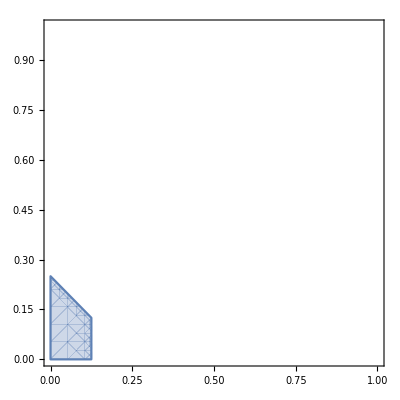

```mathematica
RegionPlot[β≥ 8α β&&β≥ 4α β+ 4β^2&&α≥ 0&&β≥0 ,{α,0,1},{β,0,1}]
```

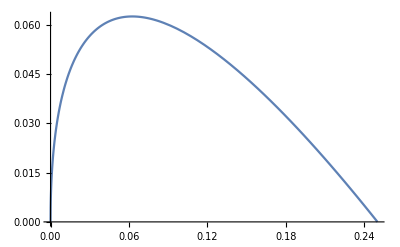

```mathematica
Plot[(√β)/2-β,{β,0,0.25}]
```